```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/rex/Desktop/dimer-dimer/dimer-dimer/dimer-1 id

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
numRAD=7;
epsi=1;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["/home/rex/LECs_lambda","Table"]
```

{{#,L[fm^-1],C_0[nucl],D_0[nucl]},{4,-505.15,1486.34},{5,-623.753},{6,-741.15,2225.34},{7,-858.067},{8,-974.604,2932.34},{9,-1090.83},{10,-1206.79,3630.34}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
ApproxDimerWF[lamd_,dimD_,nbrThreads_,nbrWidthSamples_,minW_,maxW_,minWidthDiff_,verbosity_,σw_:2]:=Block[{LECc,LECd,e0,λ=lamd,Δ=minWidthDiff,αmax=maxW,αmin=minW,Nd=dimD,Ns=nbrWidthSamples,Nth=nbrThreads},

LECc=Flatten[Select[activeLEC,#[[1]]==λ&]][[2]];
LECd=Flatten[Select[activeLEC,#[[1]]==λ&]][[3]];
Print[LECc];Print[LECd];
widths={};
rndPrec=5;
Do[

widthLr=Sort[#]&/@RandomReal[{SetPrecision[αmin,rndPrec+1],SetPrecision[αmax,rndPrec+1]},{Ns,Nd},WorkingPrecision->rndPrec];

(*t1=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmin,σw],{Ns,IntegerPart[Nd/2]}]];
t2=Sort[#]&/@Abs[RandomVariate[NormalDistribution[αmax,σw],{Ns,IntegerPart[Nd/2]}]];

widthLr=ArrayReshape[Flatten[#]&/@Tuples[{t1,t2}],{Nd,Ns}];*)

widthL=Select[widthLr,AllTrue[Select[Tuples[#,2],#[[1]]!=#[[2]]&],Abs[#[[1]]-#[[2]]]>Δ&]&];

AppendTo[widths,widthL];
,{nn,Nth}];

If[verbosity==1,Print["λ = ",λ,"   C_0(λ) = ",LECc,"  #(width-set candidates) = ",Length[Flatten[widths,1]],"  in ",Nth," parallel threads."]];
opti={};
SetSharedVariable[opti];

ta=AbsoluteTime[];
ParallelDo[
widthL=widths[[nt]];
results=0.0;e0=0.0;
optSet={};
Do[
Nd=Length[wi];
hamm=Table[ham[λ,wi[[i]],wi[[j]],LECc],{i,Nd},{j,Nd}];
normm=Table[norm[wi[[i]],wi[[j]]],{i,Nd},{j,Nd}];

{eval,evec}=Eigensystem[{hamm,normm}];

ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];

If[(
(eigsorted[[1]]<results)&&
(eigsorted[[1]]>-2.65)&&
(Im[eigsorted[[1]]]==0)&&
(NormTF[Transpose[{vecsorted[[1]],wi}]]>10^-5)&&
(Min[Abs[vecsorted[[1]]]]>10^-2)&&
(ContainsOnly[Sign[vecsorted[[1]]],{1}]||ContainsOnly[Sign[vecsorted[[1]]],{-1}])
),
(*Print[eigsorted[[1]],eigsorted];*)
e0=eigsorted[[1]];
results=eigsorted[[1]];
optSet=Transpose[{vecsorted[[1]],wi}];
]
,{wi,widthL}];
If[verbosity==1,Print["Core ",nt," : ",e0,optSet]];
AppendTo[opti,{e0,optSet}];
,{nt,Nth}];
tb=AbsoluteTime[];

e0=Sort[opti][[1]][[1]];
optSet=Sort[opti][[1]][[2]];
If[verbosity==1,Print["optimum of ",Style[Length[Flatten[widths,1]],Red,Italic,18]," candidate width sets found in Δt = ",Style[tb-ta,Red,Italic,18]," sec.          : E_0 = ",e0]];
(*Print["opt. basis: ",optSet];*)
(*Put[optSet,"dimerWF_"<>ToString[e0]<>".mmo"];
Put[e0,"E0_"<>ToString[e0]<>".mmo"];*)
{e0,optSet}
];
rma=2;rmi=0.;nR=100;
rR=Range[rmi,rma,(rma-rmi)/nR];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2)^(9/2)(Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta1,eta2,eta3,w1,w2,w3},
eta1=(3Cc Pi^1.5)/(8(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^1.5);
w1=(2lam(Aa+Bb)(Gg+Hh))/(lam Bb+Gg(lam+2Bb)+lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta2=(Pi/((lam+Aa+Bb)(lam+Gg+Hh)))^(3/2)Dd(1/2)^(9/2);
w2=(2lam(Aa+Bb))/(lam+Aa+Bb);
eta3=Pi^1.5 Dd/(8(2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh))^(3/2));
w3=(2lam (2lam+Aa+Bb)(Gg+Hh))/(2 lam^2+lam Bb+Gg(5lam+2Bb)+5lam Hh+2Bb Hh+Aa(lam+2Gg+2Hh));
eta1 Exp[-w1 r^2]+eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq,radMA},Block[{zeta1,zeta2,zeta3,zeta4,zeta5,zeta6,a1,b1,c1,a2,b2,c2,a3,b3,c3,a4,b4,c4,a5,b5,c5,a6,b6,c6,Sinh1,Sinh2,Sinh3,Sinh4,Sinh5,Sinh6,CoshA,numRAD=radMA},
zeta1=-(Pi/(2(Aa+Bb+Gg+Hh)))^(3/2)(1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(2 √2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(2 √2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta4=-(π^(3/2)/(2 √2)) Cc/(Aa +Bb+ Gg+Hh)^(3/2);
zeta5=-(Pi/(2(4lam+Aa+Bb+Gg+Hh)))^(3/2)Dd;
zeta6=-(Pi/(2(2lam+Aa+Bb+Gg+Hh)))^(3/2)Dd;

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a4= (2lam Hh+2Bb(lam+2Hh)+Gg(2lam+Bb+Hh)+Aa(Bb+2lam+Hh))/(2(Aa+Bb+Gg+Hh));
b4= (4lam Hh+4lam Bb+Gg(4lam +2Bb-2Hh)+Aa(-2Bb+4lam+2Hh))/(2(Aa+Bb+Gg+Hh));
c4=(2lam Hh+2lam Bb+Gg(2lam+Bb+Hh)+Aa(4Gg+Bb+2lam+Hh))/(2(Aa+Bb+Gg+Hh));

a5=(2lam(2lam+Hh)+2Bb(5lam+2Hh)+Gg(2lam+Bb+Hh)+Aa(Bb+2lam+Hh))/(2(4lam+Aa+Bb+Gg+Hh));
b5=(4lam(2lam+Hh)-4lam Bb+Gg(-4lam+2Bb-2Hh)+Aa(-2Bb+4lam+2Hh))/(2(4lam+Aa+Bb+Gg+Hh));
c5=(2lam(2lam+Hh)+2Bb lam+Gg(10lam+Bb+Hh)+Aa(4Gg+Bb+2lam+Hh))/(2(4lam+Aa+Bb+Gg+Hh));

a6=(2Bb(lam+2Hh)+Gg(4lam+Bb+Hh)+Aa(4lam+Bb+Hh)+2lam(2lam+5Hh))/(2(2lam+Aa+Bb+Gg+Hh));
b6=(4lam Bb+Gg(8lam+2Bb-2Hh)+Aa(-2Bb+2Hh)+2lam(4lam+2Hh))/(2(2lam+Aa+Bb+Gg+Hh));
c6=(2lam Bb+Gg(4lam+Bb+Hh)+Aa(4lam+4Gg+Bb+Hh)+2lam(2lam+Hh))/(2(2lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

(*SinhA=If[((b1!=0.0)&&(Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Sinh[b1 r rp]/b1,0.0];
SinhB=If[((b2!=0.0)&&(Abs[b2 r rp]<0.1 Abs[a2 r^2+c2 rp^2])&&(Abs[a2 r^2+c2 rp^2]<numRAD)),Exp[-a2 r^2-c2 rp^2] Sinh[b2 r rp]/b2,0.0];
SinhC=If[((b3!=0.0)&&(Abs[b3 r rp]<0.1 Abs[a3 r^2+c3 rp^2])&&(Abs[a3 r^2+c3 rp^2]<numRAD)),Exp[-a3 r^2-c3 rp^2] Sinh[b3 r rp]/b3,0.0];
CoshA=If[((Abs[b1 r rp]<0.1 Abs[a1 r^2+c1 rp^2])&&(Abs[a1 r^2+c1 rp^2]<numRAD)),Exp[-a1 r^2-c1 rp^2] Cosh[b1 r rp],0.0];*)
Sinh1=If[b1==0,0,(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1)];
Sinh2=If[b2==0,0,(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2)];
Sinh3=If[b3==0,0,(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3)];
Sinh4=If[b4==0,0,(Exp[b4 r rp-a4 r^2-c4 rp^2]-Exp[-b4 r rp-a4 r^2-c4 rp^2])/(2 b4)];
Sinh5=If[b5==0,0,(Exp[b5 r rp-a5 r^2-c5 rp^2]-Exp[-b5 r rp-a5 r^2-c5 rp^2])/(2 b5)];
Sinh6=If[b6==0,0,(Exp[b6 r rp-a6 r^2-c6 rp^2]-Exp[-b6 r rp-a6 r^2-c6 rp^2])/(2 b6)];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3+zeta4 Sinh4+zeta5 Sinh5+zeta6 Sinh6)

(*SinhA=If[b1==0.0,0.0,(Exp[-a1 r^2-c1 rp^2+b1 r rp]-Exp[-a1 r^2-c1 rp^2-b1 r rp])/(2 b1)];
SinhB=If[b2==0.0,0.0,(Exp[-a2 r^2-c2 rp^2+b2 r rp]-Exp[-a2 r^2-c2 rp^2-b2 r rp])/(2 b2)];
SinhC=If[b3==0.0,0.0,(Exp[-a3 r^2-c3 rp^2+b3 r rp]-Exp[-a3 r^2-c3 rp^2-b3 r rp])/(2 b3)];
CoshA=0.5 (Exp[-a1 r^2-c1 rp^2+b1 r rp]+Exp[-a1 r^2-c1 rp^2+b1 r rp]);*)

(*-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) SinhA-4 a1 Sqrt[3]^-1 (-r rp CoshA+SinhB))+zeta2 SinhB+zeta3 SinhC)*)
(*Chop[Exp[-a3 r^2-c3 rp^2] SinhC,10^-10]*)
]];
(*WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2Pi^1.5/(2(Aa+Bb+Gg+ Hh))^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);
zeta3=(*-(16/Pi^1.5)((Aa+Bb)(Gg+Hh) )^1.5*)-2 Pi^1.5 Cc/(2(2lam+Aa +Bb+ Gg+Hh))^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam+Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

Sinh1=(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1+100 $MachineEpsilon);
Sinh2=(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2+100 $MachineEpsilon);
Sinh3=(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3+100 $MachineEpsilon);

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];*)
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ,numR_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq,numR],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 
AppendTo[Wmats,cij (amat+wmat)];

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,LECd_,energ_:0.001,numR_]:=Module[{locall=l},

momFM=Sqrt[mh2 energ];
(*TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
TanDelSwave*){-2.20461,{{-0.00558396,0.050935},{-0.0146543,0.21000},{-0.0406902,0.99319},{-0.691399,6.2469},{0.706724,6.7867},{-0.143551,10.734}}};
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2,numR];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

-741.15

2225.34

λ = 6   C_0(λ) = -741.15  #(width-set candidates) = 39842  in 4 parallel threads.

Core 1 : -1.98466{{0.142192,0.11544},{0.386815,0.85121},{0.8357,5.0073},{0.362989,18.512}}

Core 2 : -1.33737{{0.221577,0.12541},{0.716895,1.8505},{0.443897,7.5446},{0.489817,12.321}}

Core 3 : -1.77915{{-0.0867039,0.052283},{-0.288861,0.63539},{-0.337781,1.8398},{-0.891597,8.4924}}

Core 4 : -1.71873{{0.148275,0.10855},{0.507445,1.2824},{0.846504,8.0525},{0.0628079,29.32}}

optimum of 39842 candidate width sets found in Δt = 10.8857 sec.          : E_0 = -1.98466

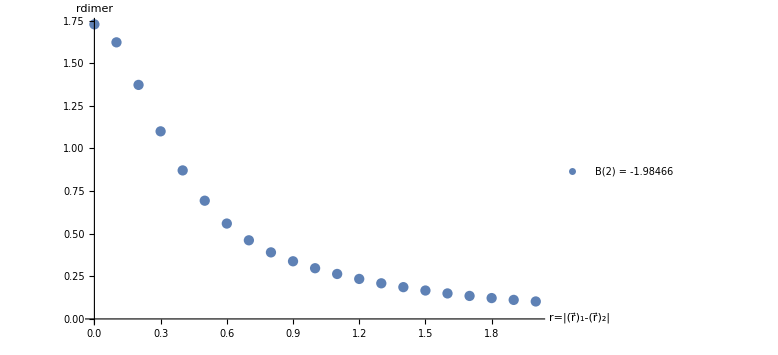

```mathematica
flag=1;

lambdaTest=6;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
dCores={};
(*WS={4.3584650 ,  2.8802200 ,  2.0651530  , 1.6563710  , 1.1615310  , 0.8261400,0.5922700  , 0.4901080 ,  0.3227900   ,0.2522220  , 0.1357500};
dCores={CalcDimerE[WS,lambdaTest,LECc]}*)

ncc=1;
If[flag>0,
Do[
{eDi,wDi}=ApproxDimerWF[lambdaTest,4,4,10000,0.001,Random[Real,{15,35}],0.01,1,2];
AppendTo[dCores,{eDi,wDi}];
,{nc,Range[ncc]}];
];

If[flag>=0,
NormTF[#]&/@dCores[[All,2]];

dCores=CalcDimerE[dCores[[#]][[2]][[All,2]],lambdaTest,LECc]&/@Range[Length[dCores]];

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;

lgd="B(2) = "<>ToString[#[[1]]]&/@dCores;
ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large]
]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.001;
(* Integration grid *)
rMa=12;
grdPerFermi=15;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,LECd,energ,numRAD][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn,"| maxE=",numRAD," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,Length[dCores]},{numRAD,{1}}];
```

Set::shape: Lists {TanDelSwave,wfkt} and SolveSecularP3[12,180,0.0069443,0,6,-741.15,LECd,{{0.142192,0.11544},{0.386815,0.85121},{0.8357,5.0073},{0.362989,18.512}},0.0482233,1] are not the same shape.

core 1| maxE=1 )  λ=6 ; C_0(λ)=-741.15 ; R_max=12 ; #=180 ; E_match=0.001 ; B(2)=-1.98466 ; dim_d=4 ; a_dd=-144.003 TanDelSwave ; a_dd/a_aa=-31.5013 TanDelSwave

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

20.7369

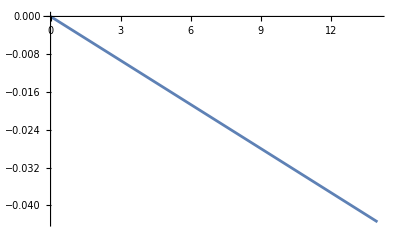

```mathematica
1/mh2
momFM=Sqrt[mh2 0.0002];
Plot[RiccatiBesselJ[momFM r,0]/RiccatiBesselN[momFM r,0](*-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin])*),{r,0,14}]
```

```mathematica
lambdaTest=10;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]]
LECd=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[3]]
```

-1206.79

3630.34

Set::write: Tag Dot in Null.7 is Protected.

0.00458949

finite-difference runtime Δt = 0.048165 mins     p_match·r_max = 0.0208329

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 3.     #(grid points) = 36                a_dd = 2.21247 fm        a_dd/a_aa = 0.505852

finite-difference runtime Δt = 0.0510712 mins     p_match·r_max = 0.024305

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 3.5     #(grid points) = 42                a_dd = 1.82431 fm        a_dd/a_aa = 0.417105

finite-difference runtime Δt = 0.0698318 mins     p_match·r_max = 0.0277772

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 4.     #(grid points) = 48                a_dd = -0.0334167 fm        a_dd/a_aa = -0.0076403

finite-difference runtime Δt = 0.0748052 mins     p_match·r_max = 0.0312493

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 4.5     #(grid points) = 54                a_dd = -10.8756 fm        a_dd/a_aa = -2.48657

finite-difference runtime Δt = 0.101816 mins     p_match·r_max = 0.0347215

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 5.     #(grid points) = 60                a_dd = 60.8288 fm        a_dd/a_aa = 13.9077

finite-difference runtime Δt = 0.136343 mins     p_match·r_max = 0.0381936

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 5.5     #(grid points) = 66                a_dd = 26.6272 fm        a_dd/a_aa = 6.08796

finite-difference runtime Δt = 0.16101 mins     p_match·r_max = 0.0416658

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 6.     #(grid points) = 72                a_dd = 29.2456 fm        a_dd/a_aa = 6.68662

finite-difference runtime Δt = 0.156808 mins     p_match·r_max = 0.0451379

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 6.5     #(grid points) = 78                a_dd = 47.1185 fm        a_dd/a_aa = 10.773

finite-difference runtime Δt = 0.182437 mins     p_match·r_max = 0.0486101

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 7.     #(grid points) = 84                a_dd = 146.996 fm        a_dd/a_aa = 33.6087

finite-difference runtime Δt = 0.201431 mins     p_match·r_max = 0.0520822

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 7.5     #(grid points) = 90                a_dd = -151.293 fm        a_dd/a_aa = -34.5911

finite-difference runtime Δt = 0.245155 mins     p_match·r_max = 0.0555544

core 1| maxE=7 )  λ = 10   C_0(λ) = -1206.79   D_0(λ) = 3630.34     R_max = 8.     #(grid points) = 96                a_dd = -62.5555 fm        a_dd/a_aa = -14.3025

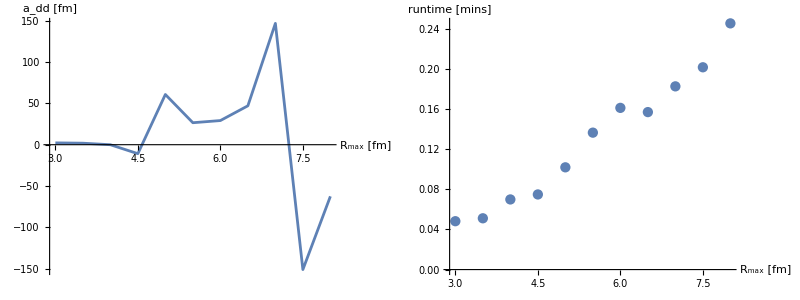

```mathematica
rMaxStart=3;
rMaxEnd=8;
nbrR=10;
coreNBR=1;
{e0Core,dimerCore}={-2.16804,{{-0.0426627,0.070543},{-0.106298,0.38188},{-0.195003,1.5780},{-0.473945,5.9320},{0.412815,10.173},{-0.744187,14.923}}};
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];
energ=0.001;
grdPerFermi=12;.
numRAD=9;
results={};
resultsWF={};
runtimes={};
NormTF[dimerCore]
(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,LECd,energ,numRAD];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,tmp2];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR,"| maxE=",numRAD," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"   D_0(λ) = ",LECd,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
```

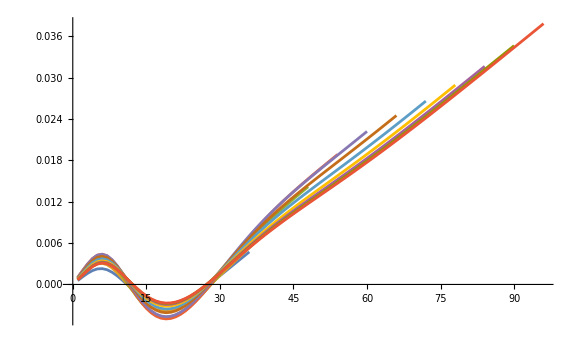

```mathematica
ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large]
```